### Categorization

Tutorial

SGD

SGD`

SGD/tutorial/Working with SGD

### Keywords

Details

# Working with SGD

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Overview of SGD

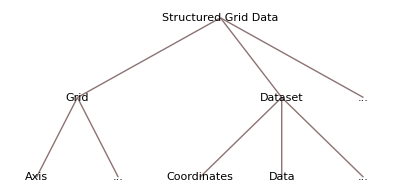

```mathematica
TreeForm["Structured Grid Data"["Grid"["Axis","..."],"Dataset"["Coordinates","Data","..."],"..."]]
```

Boxes with ... means nodes like the last brother (left to right) can be repeated. For example, a Dataset is made by {Coordinates, Data_1, Data_2, ..., Data_n} where is a positive integer.
Those repeatable components may have some metadata describing it, in the form {"metadata", data}.

The components are:
- Axis: a list of numerical vales (possibly metadated)
- Grid: a list of axis
- Data: a multidimensional array of data in a grid made by cartesian products of some axis (possibly metadated).
- Coordinates: A list of positive integers defining to which axes the subsequent Data refers.
- Dataset: a collection of Data which refers to the axes (possibly metadated).

Note that Data refering to the same axes can be splitted in different Datasets (e.g., if they are unrelated).
Sample construction:

```mathematica
Needs["SGD`"]
```

```mathematica
grid = {{"n", Table[i, {i, 0, 10, 0.2}]}, {"x", Table[i, {i, 0, 2, 0.01}]}};
```

```mathematica
dataList=Table[{ToString[f],Table[N[f[i,j]],{i,0,10,0.2},{j,0,2,0.01}]},{f,{BesselJ,BesselI,SphericalBesselJ}}];
```

```mathematica
dataset={"Bessel Funcions",{{1,2},dataList}};
```

Explore ONE dataset:

```mathematica
SGDViewDataSet[{grid,dataset}]
```

Make some interpolations

```mathematica
{f1,f2,f3}=Interpolation/@SGDGetPoints[grid,dataset]
```

{InterpolatingFunction[{{0., 10.}, {0., 2.}}, <>],InterpolatingFunction[{{0., 10.}, {0., 2.}}, <>],InterpolatingFunction[{{0., 10.}, {0., 2.}}, <>]}

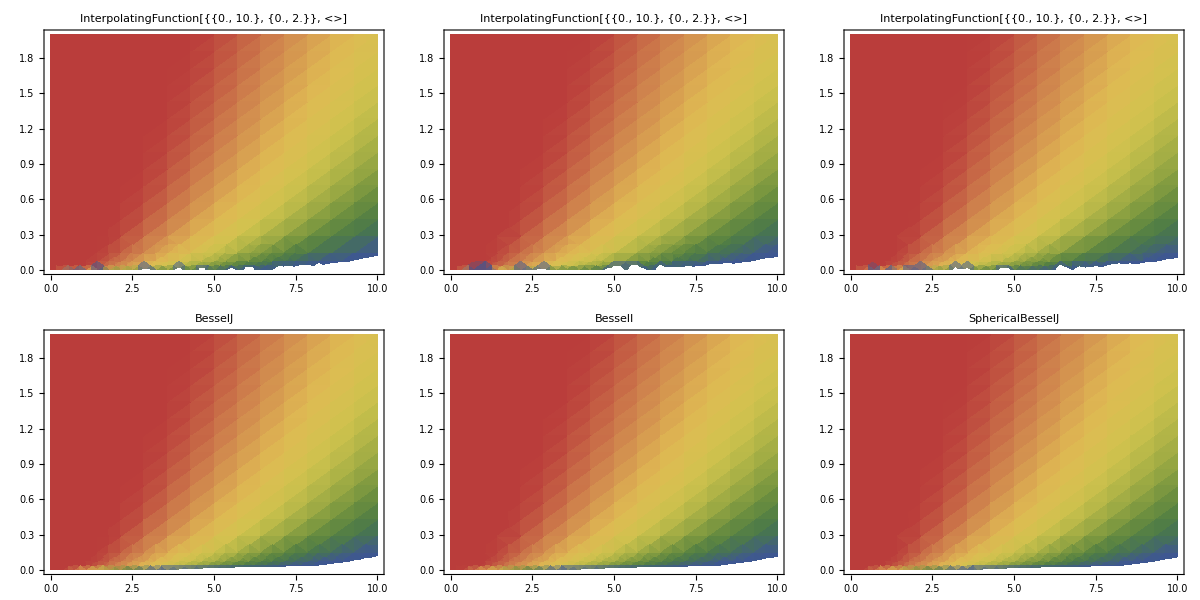

```mathematica
Map[DensityPlot[Log10[#[n,x]],{n,0,10},{x,0,2},PlotLabel->ToString[#],ColorFunction->"DarkRainbow"]&,{{f1,f2,f3},{BesselJ,BesselI,SphericalBesselJ}},{2}]//TableForm
```

More About

Related Tutorials

Related Wolfram Education Group Courses